```mathematica
sqnCalc[dat_]:=Sqrt[Length[dat]]Mean[dat]/StandardDeviation[dat]
```

```mathematica
fracChangeCalc[before_,after_]:=100((after-before)/before)
```

```mathematica
data=Delete[Import[NotebookDirectory[]<>"BTCUSDT_8h.csv"],1][[All,5]];
```

```mathematica
fracChange=Table[fracChangeCalc[data[[i]],data[[i+1]]],{i,Length[data]-1}];
```

```mathematica
movingSQN=MovingMap[sqnCalc,fracChange,Quantity[150,"Events"]];
```

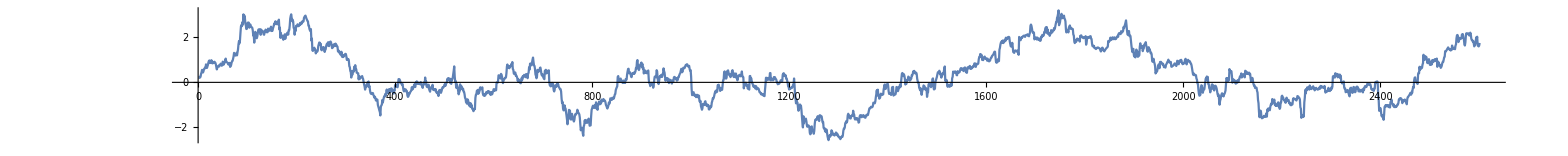

```mathematica
ListLinePlot[movingSQN, AspectRatio->0.1]
```